```mathematica
Clear["Global`*"];
θ=Function[r,2 ArcSin[Exp[-r/(2 R)]]];
n=Function[{x,y},{(Sin[θ[√(x^2+y^2)]]x)/(√(x^2+y^2)),(Sin[θ[√(x^2+y^2)]]y)/(√(x^2+y^2)),Cos[θ[√(x^2+y^2)]]}];
ρ=FullSimplify[(n[x,y].Cross[D[n[x,y],x],D[n[x,y],y]])/(4π)e];
Fρ=FullSimplify[FourierTransform[ρ,{x,y},{p,q}],Assumptions->R ∈ Reals&&R>0];
FV=Exp[-(p^2+q^2)lb^2/2]/(4 π √(p^2+q^2) ϵ);
p=r Cos[t];
q=r Sin[t];
FV=FullSimplify[FV,Assumptions->t∈Reals];
Fρ=FullSimplify[Fρ,Assumptions->t∈Reals];
EnergyD=FullSimplify[Fρ^2 FV,Assumptions->r∈Reals&&r>0];
Ec=e^2/(4π ϵ lb);
FullSimplify[(EnergyD*2π r)/Ec];
energy=FullSimplify[Integrate[EnergyD*2π r,{r,0,Infinity}],
Assumptions->R∈Reals&&R>0&&lb∈Reals&&lb>0&&md∈Reals&&md>0]

energy/Ec
R=Rr lb;
energy/Ec
```

(ⅇ^(-1/2 lb^2 r^2) lb)/(2 π+2 π r^2 R^2)

(e^2 ⅇ^(lb^2/(2 R^2)) Erfc[lb/(√2 R)])/(16 π R ϵ)

(ⅇ^(lb^2/(2 R^2)) lb Erfc[lb/(√2 R)])/(4 R)

(ⅇ^(1/(2 Rr^2)) Erfc[1/(√2 Rr)])/(4 Rr)

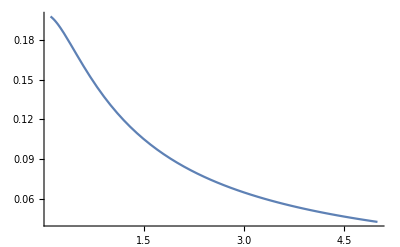

```mathematica
Plot[(ⅇ^(1/(2 Rr^2)) Erfc[1/(√2 Rr)])/(4 Rr),{Rr,0.1,5}]
```

```mathematica
R=0.8 lb;
lg=20lb;
N0=127;
ρe0=Function[{x,y},-(e ⅇ^(-(√(x^2+y^2))/R))/(2 π R √(x^2+y^2))];
ρe=Function[{x,y},ρe0[x-lg/2,y-lg/2]];
ρed=Table[ρe[lg/N0 i,lg/N0 j]*(lg/N0)^2,{i,0,N0-1},{j,0,N0-1}]
```

{{-(0.000348873 e ⅇ^(-(17.6777 √(lb^2))/lb) lb)/(√(lb^2)),-(0.000351631 e ⅇ^(-(17.539 √(lb^2))/lb) lb)/(√(lb^2)),123,-(0.00035441 e ⅇ^(-(17.4015 √(lb^2))/lb) lb)/(√(lb^2)),-(0.000351631 e ⅇ^(-(17.539 √(lb^2))/lb) lb)/(√(lb^2))},125,{-(0.000351631 e ⅇ^(-(17.539 1)/lb) lb)/(√(lb^2)),-(0.000354455 e ⅇ^(-1/lb) lb)/(√(lb^2)),-(0.000357302 e ⅇ^(-1/lb) lb)/(√(lb^2)),-(23 e11 lb)/(√(lb^2)),119,-1,-(0.000360171 e ⅇ^1 lb)/(√(lb^2)),-(0.000357302 e ⅇ^(-1/lb) lb)/(√(lb^2)),-(0.000354455 e ⅇ^(-(18 1)/lb) lb)/(√(lb^2))}}
 |  |  |  |

```mathematica
md=3;
lb=1;
R=0.8;
NIntegrate[(ⅇ^(-1/2 lb^2 r^2) lb Tanh[md r])/(2 (π+π r^2 R^2)),{r,0,Infinity}]
```

0.109922

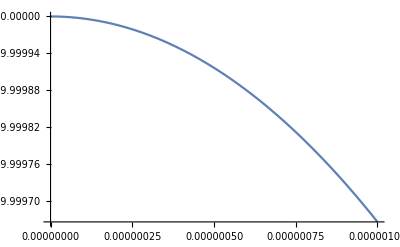

```mathematica
md=1000;
Plot[Tanh[q md]/q,{q,0,10^-6}]
```

```mathematica
Rr=0.8;
(ⅇ^(1/(2 Rr^2)) Erfc[1/(√2 Rr)])/(4 Rr)
```

0.144225

Function[md,(ⅇ^(-1/2 lb^2 r^2) lb Tanh[md r])/(2 (π+π r^2 R^2) 2 π r)]

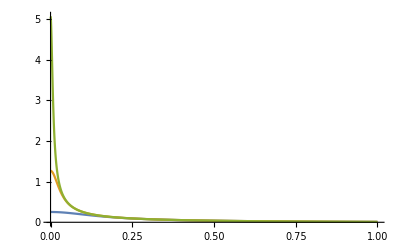

```mathematica
lb=1;
R=0.8;
md=10;
f=Function[md,(ⅇ^(-1/2 lb^2 r^2) lb Tanh[md r])/(2 (π+π r^2 R^2)2 π r)]
Plot[{f[10],f[50],f[200]},{r,0,1},PlotRange->Full]
```